## Seminarska naloga pri ROM-u Nihanje, valovanje in optika Matura 2017 - jesenski rok Otroška gugalnica je zgrajena iz dveh lahkih vrvic, na katerih je pritrjen sedež. Otrok, ki sedi na gugalnici, ima skupaj s sedežem maso 40 kg . Vrvici sta dolgi 3,0 m in sta pripeti na vejo drevesa tako, da je sedež v ravnovesni legi 50 cm nad tlemi. Privzemite, da je težišče sistema na višini sedeža. Otrok se začne poganjati in pri prvih desetih nihajih se energija nihanja poveča za 16 J pri vsakem nihaju. Po desetih nihajih se otrok poganja le še toliko, da vzdržuje stalno amplitudo nihanja. Ta je dovolj majhna, da lahko gugalnico pri vseh vprašanjih te naloge obravnavamo kot sinusno -Graphics- 1. Izračunajte nihajni čas in frekvenco nihanja gugalnice. nihajni čas:

```mathematica
Subscript[t, 0] = 2 * π * Sqrt[3 / 9.8]
```

3.47638

```mathematica
V = 1 / Subscript[t, 0]
```

0.287655

# 2. Izračunajte hitrost, s katero se po desetih nihajih otrok giblje skozi ravnovesno lego.

```mathematica
Subscript[v, 0] = N[Sqrt[2* 10 * 16   / 40]]
```

2.82843

# 3.Izračunajte, koliko časa po tem, ko se je otrok gibal skozi ravnovesno lego, je pospešek nihanja prvič enak polovici največjega pospeška.

```mathematica
t = Subscript[t, 0] / 2 * π * Sin[1 / 2]
```

2.61799

# 4.Izračunajte amplitudo odmika gugalnice od ravnovesne lege po desetih nihajih.

```mathematica
Subscript[x, 0] = V * Subscript[t, 0]/ 2 * π
```

0.451848 2.61799_0

# 5.Izračunajte kot, ki ga po desetih nihajih v skrajni legi vrvici gugalnice oklepata z navpičnico.

```mathematica
Subscript[ϕ, 0]= 1.56 / 3 * 180 / π
```

29.7938

# 6. Narišite graf časovne odvisnosti potencialne energije otroka glede na ravnovesno lego v odvisnosti od časa za vsaj dva nihajna časa nihanja gugalnice. Kot začetni trenutek na grafu izberite prehod gugalnice skozi ravnovesno lego.

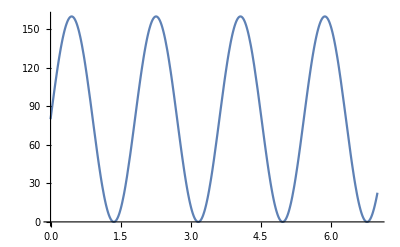

```mathematica
Plot[Sin[x / V] * 80  + 80,{x,0, 7}]
```